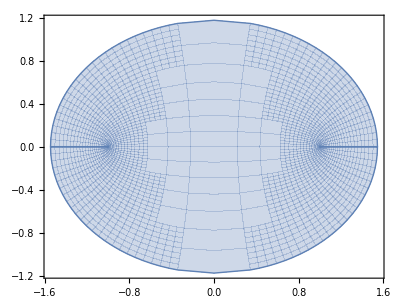

```mathematica
ParametricPlot[{Re[Sin[x+I y]], Im[Sin[x+I y]]},{x,-π/2,π/2},{y, -1, 1}]
```

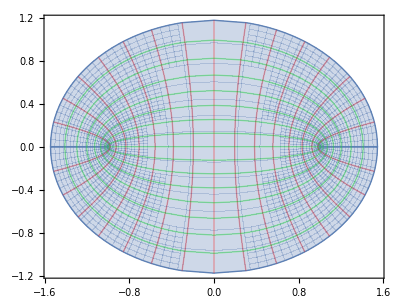

```mathematica
ParametricPlot[{Re[Sin[x+I y]], Im[Sin[x+I y]]},{x,-π/2,π/2},{y, -1, 1}, PlotRange -> Full, Mesh -> Automatic, MeshStyle->{Red,Green}]
```

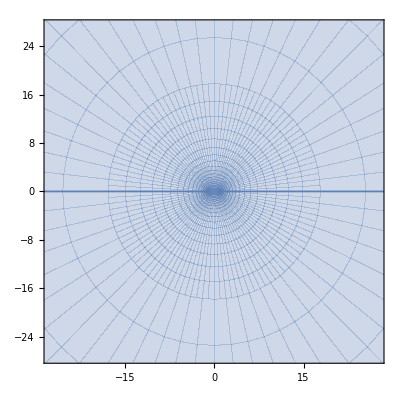

```mathematica
ParametricPlot[{Re[Sin[x+I y]], Im[Sin[x+I y]]},{x,-π/2,π/2},{y, -5, 5}]
```

```mathematica
p[s_] := ParametricPlot[{ReIm[x+I y]},{x,-Pi/2,π/2},{y, -s, s}, PlotRange -> Full, Mesh -> Automatic, MeshStyle->{Red,Green}]
```

```mathematica
q[s_] := ParametricPlot[ReIm[Sin[x+I y]],{x,-Pi/2, Pi/2},{y,-s,s},PlotRange -> Full, Mesh -> Automatic, MeshStyle->{Red,Green}]
```

```mathematica
Manipulate[{p[s], q[s]},{s,0.1,10}]
```

```mathematica
ParametricPlot[{Re[Sin[x+I y]], Im[Sin[x+I y]]},{x,-π/2,π/2},{y, -1, 1}]
```

-Graphics-

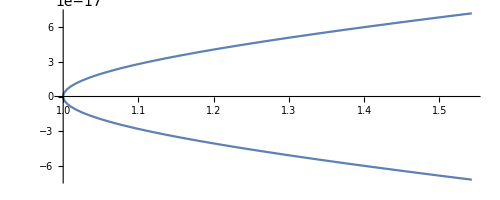

```mathematica
ParametricPlot[ReIm[Sin[π/2+I y]],{y, -1, 1}]
```

```mathematica
ParametricPlot[{Re[Sin[Pi/2 + I y]], Im[Sin[Pi/2 + I y]]},{y, -1,1}]
```

-Graphics-